```mathematica
r[n_,t_,0,a_]:=UnitStep[n-1]
r[n_,t_,k_,a_]:=Sum[j^-t r[n/j,t,k-1,a],{j,a,Floor[n]}]
```

```mathematica
r[100,1,1,8]
```

36178186814193714071499343581922991251243/13944075045942495432906761787062460711360

```mathematica
r[100,1,1,1]-HarmonicNumber[7]r[100,1,0,8]
```

36178186814193714071499343581922991251243/13944075045942495432906761787062460711360

```mathematica
Clear[s]
b[y_, s_, 0] := 1
b[1,s_,k_] := Zeta[s]^k
b[y_,s_,1]:=Zeta[s]-Zn[y,s]
bo[y_,s_,k_] := Sum[ (-1)^j Binomial[k,j] y^(-j s) Zeta[ s,y-1]^(k-j),{j,0,k}]
b[y_,s_,k_] := Sum[ (-1)^j Binomial[k,j] y^(-j s) b[y-1,s,k-j],{j,0,k}]
```

```mathematica
b[10,s,2]
```

2^(-2 s)+3^(-2 s)+4^(-2 s)+5^(-2 s)+6^(-2 s)+7^(-2 s)+8^(-2 s)+9^(-2 s)+10^(-2 s)-2^(1-s) Zeta[s]+Zeta[s]^2-2 3^-s (-1-2^-s+Zeta[s])-2^(1-2 s) (-1-2^-s-3^-s+Zeta[s])-2 5^-s (-1-2^-s-3^-s-4^-s+Zeta[s])-2^(1-s) 3^-s (-1-2^-s-3^-s-4^-s-5^-s+Zeta[s])-2 7^-s (-1-2^-s-3^-s-4^-s-5^-s-6^-s+Zeta[s])-2^(1-3 s) (-1-2^-s-3^-s-4^-s-5^-s-6^-s-7^-s+Zeta[s])-2 9^-s (-1-2^-s-3^-s-4^-s-5^-s-6^-s-7^-s-8^-s+Zeta[s])-2^(1-s) 5^-s (-1-2^-s-3^-s-4^-s-5^-s-6^-s-7^-s-8^-s-9^-s+Zeta[s])

```mathematica
Zn[s_, y_] := Sum[ j^-s,{j,1,y}]
```

```mathematica
N[Zeta[4,3+1]^2]
```

0.0000559138

```mathematica
N[Zeta[4]^2-2(Zeta[4]Zn[4,3])+(Zn[4,3])^2]
```

0.0000559138

```mathematica
N[Zeta[2,3+1]^3]
```

0.0228635

```mathematica
N[Zeta[2]^3-3(Zeta[2]^2Zn[2,3])+3(Zeta[2]Zn[2,3]^2)-(Zn[2,3])^3]
```

0.0228635

```mathematica
h[s_, y_, k_] := Sum[ (-1)^(k-j) Binomial[k,j] Zeta[s]^j Zn[s,y]^(k-j),{j,0,k}]
```

```mathematica
N[h[-1,4,4]]
```

10337.5

```mathematica
N[Zeta[-1,4+1]^4]
```

10337.5

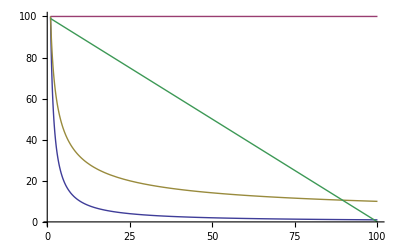

```mathematica
Plot[{100/x^1, 100/x^0, 100/x^(1/2), 100-x},{x,1,100}]
```

```mathematica
Clear[D2]
D2[n_, 0] := UnitStep[n-1]
D2[n_, k_] := D2[n,k] = Sum[ D2[Floor[n/j],k-1],{j,2,n}]
eD2[n_, z_] := Sum[ z^k/k! D2[n,k],{k,0,Log2@n}]
```

```mathematica
N@eD2[100,1]
```

303.601

```mathematica
D[gg[x,z],x]=z/(x Log[x])(gg[x,z+1]-gg[x,z])
```

Set::write: Tag D in ∂_x gg[x, z] is Protected.

(z (-gg[x,z]+gg[x,1+z]))/(x Log[x])

```mathematica
Sum[(-1)^(k+1)/(k^a)(x-1)^k,{k,1,Infinity}]
```

-PolyLog[a,1-x]

```mathematica
Sum[(-1)^(k+1)/(k^4)(x-1)^k,{k,1,Infinity}]
```

```mathematica
-PolyLog[1,1-x]
```

Log[x]

```mathematica
N[-PolyLog[a,1-8]/.a->1]
```

2.07944

```mathematica
FullSimplify[Expand[z/(x(x-1))(x^(z+1)-x^z)]]
```

x^(-1+z) z

```mathematica
D[x^z,x]
```

x^(-1+z) z

```mathematica
Log[8.]
```

2.07944

```mathematica
D[(x-1)^z,x]
```

(-1+x)^(-1+z) z

```mathematica
Expand@Integrate[ (Log[x])^4/4!,{x,1,n}]
```

ConditionalExpression[-1+n-n Log[n]+1/2 n Log[n]^2-1/6 n Log[n]^3+1/24 n Log[n]^4,Re[n]≥0||n∉Reals]

```mathematica
N@Expand[(-z Gamma[z]+Gamma[1+z,-Log[n]]) (-Log[n])^-z Log[n]^z]/.{z->5,n->100}
```

93707.7-6.88553×10^-11 ⅈ

```mathematica
Gamma[5,0,-Log[100.]]
```

-22683.1+1.38894×10^-11 ⅈ

```mathematica
Integrate[ (x-1)^4,{x,1,n}]
```

1/5 (-1+n)^5

```mathematica
Expand@Integrate[ (PolyLog[1,1-x])^4/4!,{x,1,n}]
```

ConditionalExpression[-1+n-n Log[n]+1/2 n Log[n]^2-1/6 n Log[n]^3+1/24 n Log[n]^4,Re[n]≥0||n∉Reals]

```mathematica
Expand@Integrate[ (PolyLog[2,1-x])^4/4!,{x,1,n}]
```

∫_1^n 1/24 PolyLog[2,1-x]^4ⅆx

```mathematica
Integrate[ Log[t]/t,{t,1,z}]
```

ConditionalExpression[Log[z]^2/2,Re[z]≥0||z∉Reals]

```mathematica
Integrate[ Log[t]^2/t,{t,1,z}]
```

ConditionalExpression[Log[z]^3/3,Re[z]≥0||z∉Reals]

```mathematica
Integrate[ Log[t]^3/t,{t,1,z}]
```

ConditionalExpression[Log[z]^4/4,Re[z]≥0||z∉Reals]

```mathematica
Integrate[ PolyLog[s,t]/t,{t,0,z}]
```

PolyLog[1+s,z]

```mathematica
Table[D[(-1)^z Gamma[z,0,-Log[x]]/Gamma[z],x],{z,1,8}]
```

{1,Log[x],Log[x]^2/2,Log[x]^3/6,Log[x]^4/24,Log[x]^5/120,Log[x]^6/720,Log[x]^7/5040}

```mathematica
Table[D[ (-1)^z Gamma[z, 0,-Log[x]],x],{z,1,8}]
```

{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^6,Log[x]^7}

```mathematica
Expand@Integrate[ 1, {x,1,n},{y,1,n/x},{z,1,n/(x y)}]
```

ConditionalExpression[-1+n-n Log[n]+1/2 n Log[n]^2,Re[n]≥0||n∉Reals]

```mathematica
Expand[(-1)^3 Gamma[3,0,-Log[n]]/Gamma[3]]
```

-1/2 Gamma[3,0,-Log[n]]

```mathematica
Sum[ Binomial[z,k] k/((k!)^(1/a))Integrate[Sum[(-1)^(j+1)/j^a (x-1)^j,{j,1,Infinity}]^(k-1),{x,1,n}],{k,1,Infinity}]
```

∑_(k=1)^∞ k Binomial[z,k] (k!)^(-1/a) ∫_1^n (-PolyLog[a,1-x])^(-1+k)ⅆx

```mathematica
Integrate[Sum[(-1)^(j+1)/j^a (x-1)^j,{j,1,Infinity}]^3,{x,1,n}]
```

∫_1^n -PolyLog[a,1-x]^3ⅆx

```mathematica
N@LaguerreL[5,Log[20]]
```

0.853716

```mathematica
N@20LaguerreL[-5-1,-Log[20]]
```

0.853716

```mathematica
N@Sum[ j^-2 k^-2,{j,2,n},{k,2,n}]/.n->100
```

0.403205

```mathematica
Integrate[ j^-s k^-s,{j,1,n},{k,1,n}]
```

ConditionalExpression[(n^(-2 s) (-n+n^s)^2)/(-1+s)^2,Re[n]≥0||n∉Reals]

```mathematica
N@Sum[ j^-2 k^-2 l^-2,{j,2,n},{k,2,n},{l,2,n}]/.n->100
```

0.256028

```mathematica
N@Sum[ j^-s k^-s l^-s,{j,2,n},{k,2,n},{l,2,n}]
```

(-1.+HarmonicNumber[n,s])^3

```mathematica
Sum[ (-1)^(k+1)/k (Sum[j^2,{j,2,n}])^k,{k,1,Infinity}]
```

Log[1/6 n (1+3 n+2 n^2)]

```mathematica
Expand[Sum[j,{j,2,n}]]
```

-1+n/2+n^2/2

```mathematica
-Expand[Sum[j k,{j,2,n},{k,2,n}]/2]
```

-1/2+n/2+(3 n^2)/8-n^3/4-n^4/8

```mathematica
Expand[Sum[j k l,{j,2,n},{k,2,n}, {l,2,n}]/2]
```

-1/2+(3 n)/4+(3 n^2)/8-(11 n^3)/16-(3 n^4)/16+(3 n^5)/16+n^6/16